## Approximate analytical solutions of the Schrödinger equation for the Eckart-type potential for arbitrary angular momentum

### Abstract

A number of recent papers [1-6] consider the time-independent radial Schrödinger equation, for the “Eckart-type” potential

V(r)==-α ⅇ^(-r/b)/(1-ⅇ^(-r/b))+β ⅇ^(-r/b)/((1-ⅇ^(-r/b))^2),

where α,β>0, for arbitrary angular momentum value l. This paper proposes a better approximation for the centrifugal term, l (l+1)/r^2, yielding results consistent with numerical methods.

### The Eckart Potential

First, a historical note. In 1930 Eckart [Reference] defined the one-dimensional potential

V(x)==A ⅇ^(k x)/(1+ⅇ^(k x))+B ⅇ^(k x)/((1+ⅇ^(k x))^2),

where k=2π/λ, to investigate the tunnelling through a smooth potential barrier. Here λ is the length scale over which the potential is varying.

```mathematica
Manipulate[Plot[Evaluate[ⅇ^(k x)/(1+ⅇ^(k x))+(b ⅇ^(k x))/((1+ⅇ^(k x))^2)/.x->((2 π) x)/k],{x,-3/2,3/2},PlotRange->{-0.4,1.4},Ticks->{{{-1,-λ},{1,λ}},{{0,0},{1,A}}},AxesLabel->{x,V},Filling->Axis],{{b,0,"B/A"},-3,3}]
```

Plots of the Eckart potential (Equation) as the ratio B/A varies from -3 to 3.

Qualitatively, this is very different to the “Eckart-type” potential (Equation), which is infinite at r=0.

```mathematica
V[α_,β_,b_:1][r_]:=-α ⅇ^(-r/b)/(1-ⅇ^(-r/b))+β ⅇ^(-r/b)/((1-ⅇ^(-r/b))^2)
```

```mathematica
Manipulate[Plot[Tooltip[V[α,β,b][r],α],{r,0,1},AxesLabel->{r,V},PlotRange->1000,Filling->Axis],{{α,1},0,2,Appearance->"Labeled"},{{β,0.0003},0,0.1,Appearance->"Labeled"},{{b,80},1,100,Appearance->"Labeled"},SaveDefinitions->True]
```

Plot of the “Eckart-type” potential for various α==1/b and β.

### Bound-state Solutions

The paper by Dong et al. [Reference] provides a good introduction to this topic, and a clear—albeit completely standard—treatment of the bound-state solutions. It is worth repeating that treatment here.

After factoring off the angular dependence, Ψ(r)=R(r)Y_l^m(θ,φ), the radial Schrödinger equation in atomic units reads

```mathematica
RadialSE[R_,V_][r_]=Collect[-2(-1/2(R''(r)+2/r R'(r)-(l (l+1))/r^2 R(r))+V(r)R(r)-ℰ R(r))==0,{R(r),R'(r),R''(r)},Simplify]
```

R(r) (-(l (l+1))/r^2-2 V(r)+2 ℰ)+(2 R'(r))/r+R''(r)==0

Putting R(r)=r^-1 u(r) the equation for u reads

```mathematica
Eqn[3]=Collect[-2 r RadialSE[Function[r,r^-1 u(r)],V[α,β,b]][r],{u(r),u'(r),u''(r),α,β,ℰ},Simplify]
```

u(r) (-(4 α)/(ⅇ^(r/b)-1)+(4 β ⅇ^(r/b))/((ⅇ^(r/b)-1)^2)+(2 l (l+1))/r^2-4 ℰ)-2 u''(r)==0

which is equivalent equation (3) of Dong et al. [Reference]. Scaling lengths by b (r→b ρ), energies by b^-2, and introducing 𝒜=2 b^2 α, ℬ=2 b^2 β, the scaled equation reads

```mathematica
ScaledEqn[1]=Collect[b^2 Eqn[3]/.u->Function[r,u(r/b)]/.{ℰ->ℰ/b^2,α->𝒜/(2 b^2),β->ℬ/(2 b^2)}/.r->b ρ,{u(ρ),u''(ρ),α,β,ℰ},Simplify]
```

u(ρ) (2 (-𝒜/(ⅇ^ρ-1)+(l (l+1))/ρ^2+(ⅇ^ρ ℬ)/((ⅇ^ρ-1)^2))-4 ℰ)-2 u''(ρ)==0

No analytic solution is known for this equation when l≠0. However, it is easy to obtain approximate solutions by expressing the centrifugal term, l (l+1)/r^2, in terms of functions that are “compatible” with the potential.

Introducing z=ⅇ^-ρ⟹ρ=-log(z), the scaled equation reads

```mathematica
ScaledEqn[2]=Collect[-1/2 ScaledEqn[1]/.u->Function[ρ,U(exp(-ρ))]/.ρ->-log(z),{U(z),U''(z),𝒜,ℬ,ℰ},Factor]
```

U(z) (-(l (l+1))/(log^2(z))-(𝒜 z)/(z-1)-(z ℬ)/(z-1)^2+2 ℰ)+z^2 U''(z)+z U'(z)==0

Expanding the (z-dependent part of the) centrifugal term, 1/log^2(z), into a Taylor series about z=1 one obtains,

```mathematica
1/(log^2(z))+O[z,1]^2
```

1/(z-1)^2+1/(z-1)+1/12+O((z-1)^2)

Just keeping the first term introduces a Coulomb term [Reference]. The “standard” approximation (see equation (7) of [Reference] and [Reference]) comprises the first two terms of this series. It is clear from the partial fraction expansion of the “Eckart-type” potential (Equation),

```mathematica
Apart[(z 𝒜)/(z-1)+(z ℬ)/(z-1)^2,z]
```

𝒜+(𝒜+ℬ)/(z-1)+ℬ/(z-1)^2

that this approximation is “compatible” with the potential in the sense that it is of the same form as the potential itself. Note that the “Eckart-type” potential (Equation) already has a “Coulomb” component, as is clearly seen by series expansion in ρ,

```mathematica
Series[%/.z->ⅇ^-ρ,{ρ,0,1}]
```

ℬ/ρ^2-𝒜/ρ+1/12 (6 𝒜-ℬ)-(𝒜 ρ)/12+O(ρ^2)

What is important is the quality of the approximation of the centrifugal or orbital term. The following plot shows the centrifugal term, the “standard” approximation, and the first three terms of the Taylor series, for 0≤z≤0.35.

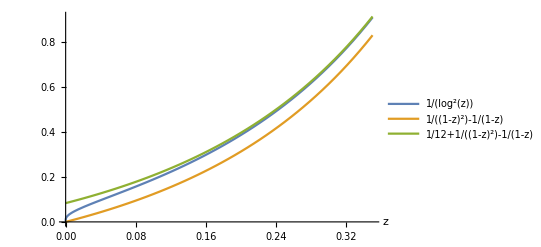

```mathematica
𝒱[z_]:={1/Log[z]^2,1/(1-z)^2-1/(1-z),1/(1-z)^2-1/(1-z)+1/12};Plot[Evaluate@𝒱[z],{z,0,0.35},AxesLabel->{z},PlotLegends->LineLegend["Expressions",LegendFunction->(Framed[#,RoundingRadius->5]&),LegendMargins->1]]
```

It is clear that taking the first three terms of the Taylor series provides an even better approximation, and that such an approximation is also “compatible” with the potential.

Using the first three terms of the Taylor series, the scaled equation reads

```mathematica
Approximation=Collect[ScaledEqn[2]/.1/(log^2(z))->Normal[1/(log^2(z))+O[z,1]^2],{U(z),U''(z)},Factor/@Apart[#,z]&]/.l^2->l (l+1)-l
```

U(z) (1/12 (-12 𝒜-l (l+1)+24 ℰ)-(𝒜+l (l+1)+ℬ)/(z-1)-(l (l+1)+ℬ)/(z-1)^2)+z^2 U''(z)+z U'(z)==0

The hypergeometric differential equation (see functions.wolfram.com/07.23.13.0001.01),

z (1-z) w''(z)+(c-(a+b+1) z) w'(z)-a b w(z)==0

has three regular singular points z=0,1,∞. Putting U(z)→z^κ (1-z)^(δ+1)w(z), the approximate scaled equation reads

```mathematica
Approximation=Collect[(Approximation/.U->Function[z,z^κ (1-z)^(δ+1)w(z)])/(z^(κ+1) (1-z)^δ),{w(z),w'(z),w''(z)},Apart[#,z]&]/.l^2->l (l+1)-l
```

w(z) (1/12 (12 𝒜-12 δ^2-24 δ κ-24 δ-12 κ^2-24 κ+l (l+1)-24 ℰ-12)+(-δ^2-δ+l (l+1)+ℬ)/(z-1)+(12 κ^2-l (l+1)+24 ℰ)/(12 z))+(z-z^2) w''(z)+w'(z) (2 κ-z (2 δ+2 κ+3)+1)==0

To get this in the form of (Equation), we put κ^2→(l (l+1))/12-2 ℰ and δ^2→l^2+l+ℬ-δ. The physical solution to this quadratic in δ is

```mathematica
Solve[l^2+l-δ^2+ℬ-δ==0,δ]//FullSimplify//Last//First
```

δ→1/2 (√((2 l+1)^2+4 ℬ)-1)

Solution of the resulting hypergeometric differential equation,

```mathematica
Approximation=(-l (l+1)+𝒜-ℬ-δ-2 δ κ-2 κ-1) w(z)+(2 κ-z (2 δ+2 κ+3)+1) w'(z)-(z-1) z w''(z)==0
```

w(z) (𝒜-2 δ κ-δ-2 κ-l (l+1)-ℬ-1)+w'(z) (2 κ-z (2 δ+2 κ+3)+1)-(z-1) z w''(z)==0

is immediate. However, introducing μ==√(δ (δ+1)+κ^2+𝒜-ℬ-l (l+1))-(δ+1), simplifies the differential equation to

```mathematica
Approximation=Collect[Expand[Approximation]/.-l^2->l+(μ+δ+1)^2-(δ^2+κ^2+𝒜-ℬ+δ),{w(z),w'(z),w''(z)},Simplify[Apart[#,z]]&]
```

w'(z) (2 κ-z (2 δ+2 κ+3)+1)-(z-1) z w''(z)-(κ-μ) w(z) (2 δ+κ+μ+2)==0

and its solution, z^κ w(z), then reads

```mathematica
Solution=z^κ w(z)/.First@DSolve[Approximation,w(z),z]/.Subscript[c, 2]->(-1)^(2 κ) Subscript[c, 2]//Expand
```

2 z^-κ -κ-μ2 δ-κ+μ+21-2 κz+1 z^κ κ-μ2 δ+κ+μ+22 κ+1z

Here c_1 and c_2 are arbitrary constants. It is clear that these two solutions are related by the interchange κ↔-κ and c_1↔ c_2. However, the solution involving z^-κ is singular at z=0 for κ≠0. The leading term in the series expansion of the other solution z^κ (1-z)^(δ+1)_2 F_1(κ-μ,2 δ+κ+μ+2;2 κ+1;z) about z=1,

```mathematica
(FullSimplify[Series[(z-1)^(δ+1)Solution/.{Subscript[c, 1]->(-1)^(1-2δ),Subscript[c, 2]->0},{z,1,0}],0<z<1]//Normal//Expand//First)/.z-1->1-z
```

(π csc(2 π δ) 2 κ+1 (1-z)^δ)/(2 δ+2 κ+μ+1 -2 δ+κ-μ-1)

is proportional to (1-z)^-δ/Γ(κ-μ), which is singular unless κ-μ==-ν for ν∈ℤ^(0+). Hence the unnormalized general solution U(z) is

```mathematica
(1-z)^(δ+1)Solution/.{Subscript[c, 1]->1,Subscript[c, 2]->0}/.μ->κ+ν
```

(1-z)^(δ+1) z^κ -ν2 δ+2 κ+ν+22 κ+1z

where δ=1/2 (√((2 l+1)^2+4 ℬ)-1), ℰ=(l (l+1))/24-κ^2/2, and

```mathematica
Solve[ν+κ==√(δ (δ+1)+κ^2+𝒜-ℬ-l (l+1))-(δ+1),κ]//FullSimplify//First//First
```

κ→-(-𝒜+2 δ ν+δ+l^2+l+(ν+1)^2+ℬ)/(2 (δ+ν+1))

Putting ν=n-l-1, the energy ℰ_(n,l) as a function of the (n,l) quantum numbers and the potential parameters 𝒜=2 b^2 α and ℬ=2 b^2 β reads

```mathematica
Subscript[ℰ, n_,l_][𝒜_,ℬ_]=(l (l+1))/24-κ^2/2/.κ->-(l^2+l+(ν+1)^2-𝒜+ℬ+δ+2 δ ν)/(2 (δ+ν+1))/.δ->1/2 (√((2 l+1)^2+4 ℬ)-1)/.ν->n-l-1//Simplify
```

1/24 l (l+1)-((-𝒜+l^2+(-l+n-1) (√((2 l+1)^2+4 ℬ)-1)+(l-n)^2+1/2 (√((2 l+1)^2+4 ℬ)-1)+l+ℬ)^2)/(8 (1/2 (√((2 l+1)^2+4 ℬ)-1)-l+n)^2)

Rewriting this in terms of the potential parameters α, β, and the scale parameter b, one has

```mathematica
Subscript[ℰ, n_,l_][α_,β_,b_]=1/b^2 Subscript[ℰ, n,l](2 b^2 α,2 b^2 β);
```

The case β=0 — the Hulthén potential — reduces to

```mathematica
1/(24 b^2) l (l+1)+FullSimplify[Subscript[ℰ, n,l][α,0,b]-1/(24 b^2) l (l+1),l>0]
```

(l (l+1))/(24 b^2)-((n^2-2 α b^2)^2)/(8 b^2 n^2)

```mathematica
data[n_,l_]:=Module[{dat=Table[Flatten[{SetAccuracy[α,4],SetAccuracy[Table[-Subscript[ℰ, n,l][α,β,1/α],{β,{0.00005,0.0001}}],7]}],{α,Join[0.025 Range[4],0.05 Range[3,7]]}],neg},neg=Position[dat,x_/;x<0];If[neg==={},dat,Take[dat,First[Union[First/@neg]]-1]]];
header={{"α \\ β",0.00005,0.0001}};
Grid[Table[Grid[{{n,l,Grid[ArrayFlatten[{{header},{data[n,l]}}],Dividers->{{2->True},{2->True}}]}}],{n,2,6},{l,1,n-1}],Spacings->{2,2}]
```

2 | 1 | α \ β | 0.00005 | 0.0001
0.025 | 0.106474 | 0.100836
0.05 | 0.099415 | 0.097835
0.075 | 0.089124 | 0.088414
0.1 | 0.078768 | 0.078373
0.15 | 0.059207 | 0.059039
0.2 | 0.041579 | 0.041492
0.25 | 0.025992 | 0.025942
0.3 | 0.01247 | 0.012441
0.35 | 0.001024 | 0.001007 |  |  |  | 
3 | 1 | α \ β | 0.00005 | 0.0001
0.025 | 0.04184 | 0.040125
0.05 | 0.032696 | 0.032243
0.075 | 0.023722 | 0.02353
0.1 | 0.015874 | 0.015777
0.15 | 0.003963 | 0.003934 | 3 | 2 | α \ β | 0.00005 | 0.0001
0.025 | 0.042458 | 0.041364
0.05 | 0.032463 | 0.032187
0.075 | 0.022861 | 0.022745
0.1 | 0.014247 | 0.014188
0.15 | 0.000225 | 0.000207 |  |  | 
4 | 1 | α \ β | 0.00005 | 0.0001
0.025 | 0.019178 | 0.018462
0.05 | 0.010869 | 0.010699
0.075 | 0.004472 | 0.004414
0.1 | 0.000398 | 0.00038 | 4 | 2 | α \ β | 0.00005 | 0.0001
0.025 | 0.019373 | 0.018919
0.05 | 0.010521 | 0.010417
0.075 | 0.003558 | 0.003523 | 4 | 3 | α \ β | 0.00005 | 0.0001
0.025 | 0.019349 | 0.019018
0.05 | 0.009925 | 0.009851
0.075 | 0.002162 | 0.002137 |  | 
5 | 1 | α \ β | 0.00005 | 0.0001
0.025 | 0.009029 | 0.008682
0.05 | 0.00254 | 0.002477 | 5 | 2 | α \ β | 0.00005 | 0.0001
0.025 | 0.00907 | 0.00885
0.05 | 0.002149 | 0.00211 | 5 | 3 | α \ β | 0.00005 | 0.0001
0.025 | 0.008977 | 0.008818
0.05 | 0.001535 | 0.001507 | 5 | 4 | α \ β | 0.00005 | 0.0001
0.025 | 0.008805 | 0.00868
0.05 | 0.000708 | 0.000686 | 
6 | 1 | α \ β | 0.00005 | 0.0001
0.025 | 0.003959 | 0.003781 | 6 | 2 | α \ β | 0.00005 | 0.0001
0.025 | 0.003929 | 0.003817 | 6 | 3 | α \ β | 0.00005 | 0.0001
0.025 | 0.003805 | 0.003724 | 6 | 4 | α \ β | 0.00005 | 0.0001
0.025 | 0.003615 | 0.003551 | 6 | 5 | α \ β | 0.00005 | 0.0001
0.025 | 0.003367 | 0.003314

Energy eigenvalues -ℰ_(n,l) for 1≤l<n≤6.

### Variational Energies

To assess the quality of these results, it is straightforward to compute accurate energy eigenvalues using standard variational methods. Using integration by parts, the radial Schrödinger equation can be rewritten as

-2 ℰ ⟨R|R⟩==⟨∂_r R|∂_r R⟩+l (l+1)⟨R|1/r^2|R⟩-2α ⟨R|ⅇ^(-r/b)/(1-ⅇ^(-r/b))|R⟩+2β ⟨R|ⅇ^(-r/b)/((1-ⅇ^(-r/b))^2)|R⟩

where the required matrix elements can be computed directly as numerical integrals,

```mathematica
⟨ψ_|φ_⟩:=NIntegrate[ψ φ r^2,{r,0,∞}]
```

```mathematica
𝒩[f_,g_]:=⟨f|g⟩
```

```mathematica
⟨ψ_|x_|φ_⟩:=NIntegrate[ψ x φ r^2,{r,0,∞}]
```

Introducing the matrix element,

```mathematica
⟨l_,α_,β_⟩[ψ_,φ_]:=⟨D[ψ, r]|D[φ, r]⟩+l (l+1)⟨ψ|1/r^2|φ⟩-2α ⟨ψ|ⅇ^(-α r)/(1-ⅇ^(-α r))|φ⟩+2β ⟨ψ|ⅇ^(-α r)/((1-ⅇ^(-α r))^2)|φ⟩
```

and using hydrogenic radial wave functions,

```mathematica
Subscript[R, n_,l_,Z_:1](r_)=r^l ⅇ^(-(Z r)/n) Subscript[L, n-l-1]^(2 l+1)((2 Z r)/n);
```

with 0≤l<n≤5 as the basis set,

```mathematica
fs=Flatten@Table[Subscript[R, n,l](r),{n,1,5},{l,0,n-1}]
```

{ⅇ^-r,ⅇ^(-r/2) (2-r),ⅇ^(-r/2) r,1/9 ⅇ^(-r/3) (2 r^2-18 r+27),ⅇ^(-r/3) (4-(2 r)/3) r,ⅇ^(-r/3) r^2,1/48 ⅇ^(-r/4) (-r^3+24 r^2-144 r+192),1/8 ⅇ^(-r/4) r (r^2-20 r+80),ⅇ^(-r/4) (6-r/2) r^2,ⅇ^(-r/4) r^3,(ⅇ^(-r/5) (2 r^4-100 r^3+1500 r^2-7500 r+9375))/1875,-2/375 ⅇ^(-r/5) r (2 r^3-90 r^2+1125 r-3750),1/25 ⅇ^(-r/5) r^2 (2 r^2-70 r+525),ⅇ^(-r/5) (8-(2 r)/5) r^3,ⅇ^(-r/5) r^4}

here are the results for -ℰ_(n,l) for n=2,…,6 with l=1, α=0.025, and β=0.0001:

```mathematica
Cases[Eigenvalues[{Outer[⟨1,0.025,0.0001⟩,fs,fs],-2Outer[𝒩,fs,fs]}]//Quiet//Chop//Sort//Reverse,e_Real/;e>0]
```

{2.38329,0.100835,0.0401248,0.0184631,0.00868422,0.00333222}

Apart from -ℰ_(6,1) these values agree with Lucha and Schöberl [Reference] and are consistent with the approximate energies computed above (indicated in bold in Table 1).

The variational energies -ℰ_(2,1) with α=0.35, β=0.00005, and β=0.0001,

```mathematica
Table[Cases[Eigenvalues[{Outer[⟨1,0.35,β⟩,fs,fs],-2Outer[𝒩,fs,fs]}]//Quiet//Chop//Sort//Reverse,e_Real/;e>0],{β,{0.00005,0.0001}}]
```

(3.09629 | 0.00377804
3.08768 | 0.00376298)

are consistent with those of Lucha and Schöberl [Reference].

### Pre-requisites

We modify Equal so that Listable operations are automatically applied to both sides of any equality:

```mathematica
Unprotect[Equal];
```

```mathematica
listableQ[f_]:=MemberQ[Attributes[f],Listable]
```

```mathematica
Equal/:lhs:f_Symbol?listableQ[___,_Equal,___]:=Thread[Unevaluated[lhs],Equal]
```

```mathematica
Protect[Equal];
```

Now, we can directly manipulate equations.

## References

[Reference] Dong S H, Qiang W C, Sun G H and Bezerra V B 2007 J. Phys. A 40 10535

[Reference] Chen C Y, Sun D S and Lu F L 2008 J. Phys. A 41 035302

[Reference] Chen C Y, Lu F L and Sun D S 2007 Phys. Scr. 76 428

[Reference] Qiang W C and Dong S H 2007 Phys. Lett. A 368 13

[Reference] Dong S, García-Ravelo J and Dong S H 2007 Phys. Scr. 76 393-396

[Reference] Wei G F, Long C Y, Duan X Y and Dong S H 2008 Phys. Scr. 77 035001

[Reference] Eckart C 1930 Phys. Rev. 35 1303

[Reference] Lucha W and Schöberl F F 1999 Int. J. Mod. Phys. C 10 607